## Solar surface probability

```mathematica
$Assumptions=mol>0&&cm>0&&m>0&&eV>0&&MeV>0;
```

```mathematica
SSModel = Import[NotebookDirectory[]<>"Data/bs2005agsopflux.txt","Table"];
data=SSModel[[28;;,;;]];
```

```mathematica
MatrixForm[SSModel[[1;;27]]]
```

({Distribution,of,neutrino,fluxes,in,the,BS05(AGS,OP),standard,solar,model,model.}
{}
{astro-ph/0412440}
{}
{The,cumulative,neutrino,fluxes,from,Table,1,of,BS05(AGS,OP),are,given,in,the,row,below.}
{}
{6.058,0.01453,8.254×10^-7,0.4338,0.0004508,0.02007,0.01445,0.0003254}
{}
{}
{Columns,in,the,Table,below,represent:}
{}
{1),Radius,of,the,zone,in,units,of,one,solar,radius}
{2),Temperature,in,units,of,10^6,deg,(K)}
{3),Logarithm,(to,the,base,10),of,the,electron,density,in,units,of}
{cm^{-3}/N_A,,where,N_A,is,the,Avogadro,number}
{4),Mass,of,the,zone,with,the,given,radius,in,units,of,one,solar,mass}
{5),X(^7Be):,beryllium-7,mass,fraction}
{[For,special,purposes,,it,is,useful,to,know,the,7^Be,mass,fraction.]}
{6),Fraction,of,pp,neutrinos,produced,in,the,zone}
{7),Fraction,of,boron,8,neutrinos,produced,in,the,zone}
{8),Fraction,of,nitrogen,13,neutrinos,produced,in,the,zone}
{9),Fraction,of,oxygen,15,neutrinos,produced,in,the,zone}
{10),Fraction,of,florine,17,neutrinos,produced,in,the,zone}
{11),Fraction,of,beryllium,7,neutrinos,produced,in,the,zone}
{12),Fraction,of,pep,neutrinos,produced,in,the,zone}
{13),Fraction,of,hep,neutrinos,produced,in,the,zone}
{})

```mathematica
B8data = Import[NotebookDirectory[]<>"Data/B8.csv"];
B8 = Interpolation[B8data,InterpolationOrder->1];
HEPdata = Import[NotebookDirectory[]<>"Data/HEP.csv"];
HEP = Interpolation[HEPdata,InterpolationOrder->1];

density[r_] = Interpolation[Table[{data[[i,1]],10^data[[i,3]]},{i,Length[data]}],InterpolationOrder->1][r]*(mol/cm^3);

B8radial = Interpolation[data[[All,{1,7}]],InterpolationOrder->1];
B8int = NIntegrate[B8radial[r],{r,0,0.5}];
HEPradial = Interpolation[data[[All,{1,13}]],InterpolationOrder->1];
HEPint = NIntegrate[HEPradial[r],{r,0,0.5}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.000409837 and 9.97523×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.141594}. NIntegrate obtained 0.000409834 and 9.25407×10^-10 for the integral and error estimates.

```mathematica
V[Ne_] := (3.868 10^-7/m)*(Ne/(mol/cm^3)); (* 4.17 in 1802.05781 *)
k[Δm2_,e_]:= (2.533/m)*(Δm2/eV^2)*(MeV/e); (* 4.18 in 1802.05781 *)
```

```mathematica
th12M[th12_,th13_, Δms21_,Δms31_,e_,Ne_] := Mod[ArcTan[Tan[2 th12]/(1 - (Cos[th13]^2/Cos[2 th12])* (V[Ne]/k[Δms21,e]) )]/2,Pi/2];
th13M[th12_,th13_, Δms21_,Δms31_,e_,Ne_] := Mod[ArcSin[Sin[th13]*(1+ (V[Ne]/k[Δms31,e])*Cos[th13]^2)],Pi/2];
```

```mathematica
Pveve[th12_,th13_, Δms21_,Δms31_,e_,Ne_]:=Cos[th13]^2 Cos[th13M[th12,th13, Δms21,Δms31,e,Ne]]^2*(Cos[th12]^2 Cos[th12M[th12,th13, Δms21,Δms31,e,Ne]]^2 + Sin[th12]^2 Sin[th12M[th12,th13, Δms21,Δms31,e,Ne]]^2) + Sin[th13]^2 Sin[th13M[th12,th13,Δms21,Δms31,e,Ne]]^2;
```

```mathematica
PB8=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8data[[All,1]]}];
Phep=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*HEPradial[r]/HEPint,{r,0,0.5}]},{e,HEPdata[[All,1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.524036 and 1.03833×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.519144 and 1.09452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.514518 and 1.07358×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.53592 and 1.1541×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.531832 and 1.25797×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.528817 and 1.30858×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

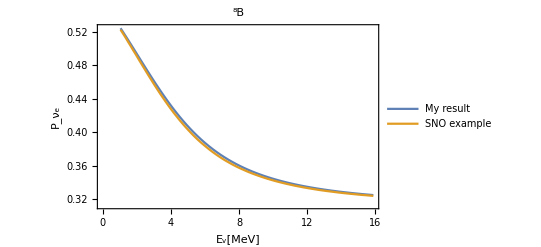

```mathematica
ListPlot[{PB8,B8data},Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"^8B",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

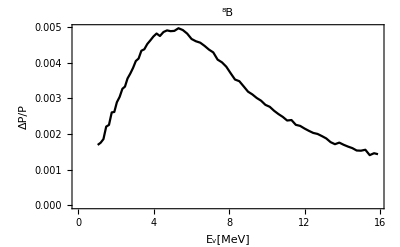

```mathematica
ListPlot[Table[{PB8[[i,1]],Abs[((PB8-B8data)/(PB8+B8data))[[All,2]][[i]]]},{i,Length[PB8]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"^8B",PlotStyle->Black]
```

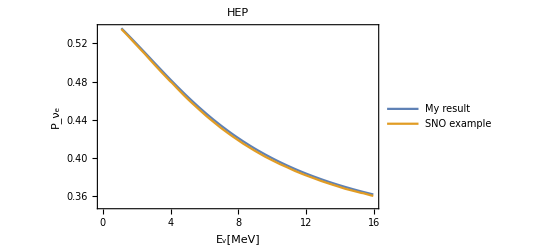

```mathematica
ListPlot[{Phep,HEPdata},Joined->True,Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"HEP",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

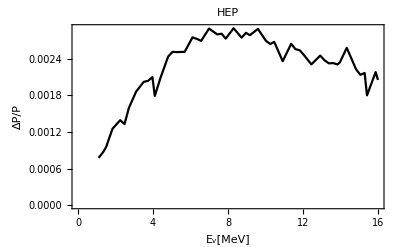

```mathematica
ListPlot[Table[{Phep[[i,1]],Abs[((Phep-HEPdata)/(Phep+HEPdata))[[All,2]][[i]]]},{i,Length[Phep]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"HEP",PlotStyle->Black]
```

## Earth regeneration

#### Earth and detector radii

```mathematica
rE = 6.371*10^6 ; (* m *)
rDet =rE- 2 10^3 ; (* m *)
```

#### Earth' s density parametrization: 9702343

```mathematica
α={6.099, 5.803, 3.156, -5.376, 11.540};
β = {-4.119, -3.653, -1.459, 19.210, -20.280};
γ = {0, -1.086, 0.280, -12.520, 10.410};
rj = {0, 0.192, 0.546, 0.895, 0.937, 1};
```

Electron density

```mathematica
Ne[r_]=Piecewise[Table[{α[[i]] + β[[i]] r^2 + γ[[i]] r^4,rj[[i]]≤r<rj[[i+1]]},{i,Length[rj]-1}]];
```

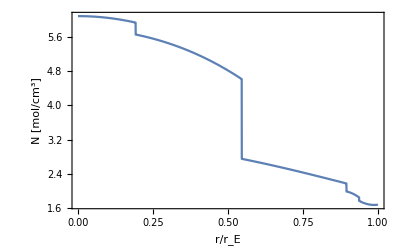

```mathematica
Plot[Ne[r],{r,0,1},Exclusions->None, Frame->True, FrameLabel->{"r/r_E", "N [mol/cm^3]"}]
```

Select the shells that are crossed as a function of the nadir angle η, and the density profile on the related path: 9702343

```mathematica
idx[η_] := Flatten[Position[rj,_?(#>Sin[η]&)]];

αp[η_]:=α[[idx[η]-1]] + β[[idx[η]-1]] Sin[η]^2 + γ[[idx[η]-1]] Sin[η]^4;
βp[η_] := β[[idx[η]-1]] + 2 γ[[idx[η]-1]] Sin[η]^2;
γp[η_] := γ[[idx[η]-1]];
```

Compute the boundaries xj of the crossed shells as a function of the nadir angle η

```mathematica
xj[η_] :=Which[0≤η<Pi/2,Prepend[√(rj[[idx[η]]]^2 - Sin[η]^2),0],Pi/2≤η≤Pi,{0}];
```

Compute the contribution in length Δx of the shell outside the detector radius

```mathematica
Δx[η_] := Piecewise[{{- rDet Cos[η] + √(rE^2-rDet^2 Sin[η]^2),0≤η<Pi/2},{ rDet Cos[η] + √(rE^2-rDet^2 Sin[η]^2),Pi/2≤η≤Pi}}]
```

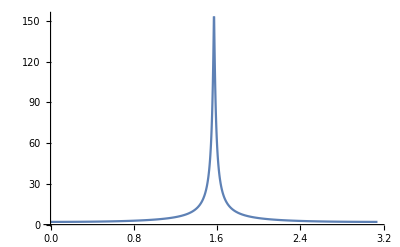

```mathematica
Plot[Δx[η]/10^3,{η,0,Pi},PlotRange->Full]
```

Compute the density along the chord with nadir angle η:

```mathematica
Nchord[η_, x_] := Which[0≤η<Pi/2,Piecewise[Table[{αp[η][[i]] + βp[η][[i]] x^2 + γp[η][[i]] x^4,xj[η][[i]]≤x<xj[η][[i+1]]},{i,Length[xj[η]]-1}]],
Pi/2≤η≤Pi,Ne[rDet/rE]]
```

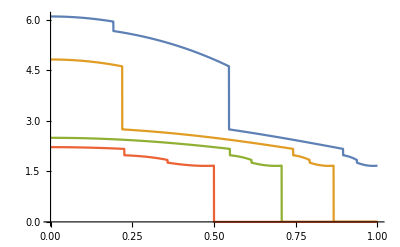

```mathematica
Plot[{Nchord[0,x],Nchord[30 Degree,x],Nchord[45 Degree,x],Nchord[60 Degree,x]},{x,0,1},Exclusions->None]
```

Compute the integrated density on each shell

```mathematica
Nint[η_] := Module[{x=xj[η]},Which[0≤η<Pi/2,Append[Table[(αp[η][[i]](x[[i+1]]-x[[i]])  + (βp[η][[i]] (x[[i+1]]^3-x[[i]]^3))/3 + (γp[η][[i]] (x[[i+1]]^5-x[[i]]^5))/5),{i,Length[xj[η]]-1}], Ne[rDet/rE] Δx[η]/rE],Pi/2≤η≤Pi,Ne[rDet/rE] Δx[η]/rE]]
```

```mathematica
(* 3 flavour formalism, only NO for now *)
```

Define PMNS mixing matrix

```mathematica
R23[th23_] := {{1,0,0},{0, Cos[th23],Sin[th23]},{0,-Sin[th23],Cos[th23]}};
R13[th13_] := {{Cos[th13],0,Sin[th13]},{0, 1,0},{-Sin[th13],0,Cos[th13]}};
R12[th12_] := {{Cos[th12],Sin[th12],0},{-Sin[th12],Cos[th12],0},{0,0,1}};
Δ[δ_]:= DiagonalMatrix[{1,1,Exp[I δ]}];
```

```mathematica
PMNS[th12_,th13_,th23_,δ_]:=R23[th23].Δ[δ].R13[th13].Δ[δ]*.R12[th12];
```

First order in Magnus expansion

```mathematica
Htilde0[th13_,th12_,Δms21_,Δms3l_,E_]:=Module[{r13 = R13[th13],r12=R12[th12]},
r13.r12.DiagonalMatrix[{0,k[Δms21,E], k[Δms3l,E]}].r12ᵀ.r13ᵀ];
```

Compute second order term in Magnus expansion

```mathematica
h[x_]:=R13[Th13].R12[Th12].DiagonalMatrix[{0,k2,k3}].R12[Th12]ᵀ.R13[Th13]ᵀ + DiagonalMatrix[{v[x],0,0}];
comm[a_,b_]:=Simplify[a.b-b.a];
```

```mathematica
FullSimplify[comm[h[x],h[y]]/(v[x]-v[y])]
```

{{0,k2 Cos[Th12] Cos[Th13] Sin[Th12],1/4 (-k2+2 k3+k2 Cos[2 Th12]) Sin[2 Th13]},{-k2 Cos[Th12] Cos[Th13] Sin[Th12],0,0},{1/4 (k2-2 k3-k2 Cos[2 Th12]) Sin[2 Th13],0,0}}

```mathematica
(* We use k2(Cos[2 th12]-1) = - 2 k2 Sin[th12]^2 *)

Htilde2[th13_,th12_,Δms21_,Δms3l_,E_]:=Module[{h12=k[Δms21,E] Cos[th12]Cos[th13]Sin[th12],h13=((-k[Δms21,E]Sin[th12]^2+ k[Δms3l,E])Sin[2th13])/2},
{{0,h12 ,h13},{-h12,0,0},{-h13,0,0}}]
```

Obtain simpler analytical for for the integral

```mathematica
v[x_]:=a + b x^2 + c x^4;
Simplify[Integrate[v[x]-v[y],{x,x1,x2},{y,x1,x}]]
```

-1/30 (x1-x2)^3 (x1+x2) (5 b+2 c (2 x1^2+x1 x2+2 x2^2))

Second order in Magnus expansion

```mathematica
densityMagnus2[η_]:=Module[{x=xj[η]},-1/30 Table[(x[[i]]-x[[i+1]])^3 (x[[i]]+x[[i+1]]) (5 βp[η][[i]]+2 γp[η][[i]] (2 x[[i]]^2+x[[i]]* x[[i+1]]+2 x[[i+1]]^2)),{i,Length[xj[η]]-1}]];
```

Matter - dependent evolutor at 2nd order in Magnus expansion

```mathematica
Utilde[th13_,th12_,Δms21_,Δms3l_,E_,η_] := Module[{x=xj[η],h0 = Htilde0[th13,th12,Δms21,Δms3l,E],h2 = Htilde2[th13,th12,Δms21,Δms3l,E],dens=densityMagnus2[η]},
Which[0≤η<Pi/2,Table[MatrixExp[-I rE*( h0 (x[[i+1]]-x[[i]]) +DiagonalMatrix[{ V[Nint[η][[i]]*mol/cm^3],0,0}])-(rE V[dens[[i]]*mol/cm^3]*h2)/2],{i,Length[xj[η]]-1}],
Pi/2≤η≤Pi,MatrixExp[-I rE((Δx[η]/rE)*h0 +DiagonalMatrix[{ V[Nint[η]*mol/cm^3],0,0}])]]]
```

```mathematica
(* Now add full expression for the evolutor U *)
```

```mathematica
th12=33.44 Degree;
th23=49 Degree;
th13=8.57 Degree;
d = 195 Degree;
dm12= 7.42 10^-5 eV^2;
dm3l=2.514 10^-3 eV^2;
```

```mathematica
r23 := R23[th23];
Delta := Δ[d];
```

```mathematica
Htilde[th13_,th12_,Δms21_,Δms3l_,E_, n_] := Module[{r13=R13[th13],r12=R12[th12]},Chop[m*(r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ+DiagonalMatrix[{V[n],0,0}])]]
```

```mathematica
(* Set m=1 to solve numerical equation *)
m=1;
```

Density along a crossed path

```mathematica
Ncross[eta_,x_]:=Piecewise[{{Nchord[eta,x],x≥0},{Nchord[eta,-x],x<0}}]
```

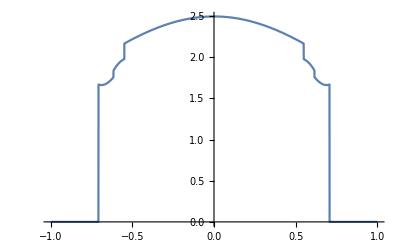

```mathematica
Plot[Ncross[45 Degree,x],{x,-1,1},Exclusions->None]
```

Test agreement of Magnus expansion with numerical evolution

```mathematica
eta=RandomReal[{0,180}] Degree;
energy = RandomReal[{1,20}] MeV;
{eta/Degree, energy}
t=Which[0≤eta<Pi/2,Last[xj[eta]],Pi/2≤eta≤Pi,Δx[eta]/rE];
i=1;
{t1,t2} = {-Last[xj[eta]],Last[xj[eta]]};
s = Timing[NDSolve[{D[{nue[x],numu[x],nutau[x]},x] == - I(rE*m*r23.Delta.Htilde[th13,th12,dm12, dm3l ,energy,Ncross[eta,x]mol/cm^3 ].Delta*.r23ᵀ).{nue[x],numu[x],nutau[x]},{nue[t1],numu[t1],nutau[t1]}==PMNS[th12,th13,th23,d][[;;,2]]},{nue,numu,nutau},{x,t1,t2}]]
s=s[[2]];
```

{43.9813,6.60549 MeV}

{0.86208,{{nue→InterpolatingFunction[{{-0.719566, 0.719566}}, <>],numu→InterpolatingFunction[{{-0.719566, 0.719566}}, <>],nutau→InterpolatingFunction[{{-0.719566, 0.719566}}, <>]}}}

```mathematica
{eta,Cos[Pi-eta]}
```

{0.767619,-0.719566}

```mathematica
Evaluate[{nue[t2],numu[t2],nutau[t2]}/.s]
Abs[%]^2
```

{{0.458177+0.295391 ⅈ,0.500287+0.344864 ⅈ,-0.491344-0.303612 ⅈ}}

{{0.297182,0.369219,0.333599}}

```mathematica
Timing[temp=Utilde[th13,th12,dm12, dm3l,energy,eta];
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]])]
Abs[%[[2]]]^2
```

{0.052889,{0.457443+0.296283 ⅈ,0.500459+0.344445 ⅈ,-0.49179-0.303321 ⅈ}}

{0.297038,0.369102,0.33386}

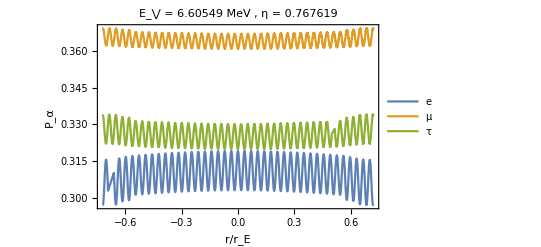

```mathematica
Plot[Evaluate[Abs[{nue[x],numu[x],nutau[x]}/.s]^2],{x,t1,t2},PlotLegends->{"e","μ","τ"}, Frame->True, FrameLabel->{"r/r_E","P_α"},PlotLabel->"E_⋁ = "<>ToString[energy]<>" ,  η = "<>ToString[eta]]
```

Here I change the oscillation parameters to reproduce a SNO example

```mathematica
th12 = √ArcTan[0.469];
th13 = √ArcSin[0.01];
dm12 = 7.9 10^-5 eV^2;
dm3l = 2.46 10^-3 eV^2;
```

```mathematica
B8dataHorizon = Import[NotebookDirectory[]<>"Data/B8horizon.csv"];
PB8new=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8dataHorizon[[All,1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.525076 and 1.09284×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.519992 and 1.15751×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.515635 and 1.06582×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
PeesolarHorizon[energy_] := Module[{temp=MatrixExp[-I rE((Δx[Pi/2]/rE)*Htilde0[th13,th12,dm12,dm3l,energy MeV] +DiagonalMatrix[{ V[1.35*Δx[Pi/2]/rE*mol/cm^3],0,0}])]},
Abs[(r23.Delta.temp.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]]))[[1]]]^2];
```

```mathematica
avgcos2th12[e_]:=NIntegrate[Cos[2 th12M[th12,th13, dm12,dm3l,e*MeV,density[r]]]*B8radial[r],{r,0,0.5}]/B8int;
```

```mathematica
Night[e_] :=-Cos[th13]^2 * avgcos2th12[e]*(PeesolarHorizon[e] - Abs[PMNS[th12,th13,th23,d][[1,2]]]^2);
```

```mathematica
PB8horizon= Table[{PB8new[[i,1]],PB8new[[i,2]] + Night[PB8new[[i,1]]]},{i, Length[PB8new]} ];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.000029626 and 1.08359×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.0000178116 and 1.19959×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 7.79343×10^-6 and 1.25032×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

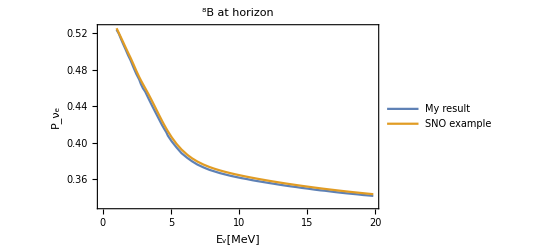

```mathematica
ListPlot[{B8dataHorizon,PB8horizon},Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"^8B at horizon",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

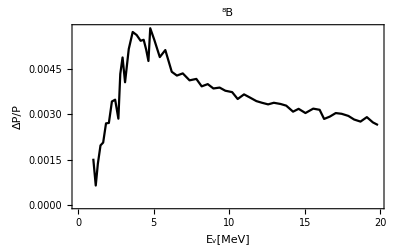

```mathematica
ListPlot[Table[{PB8horizon[[i,1]],Abs[((PB8horizon-B8dataHorizon)/(PB8horizon+B8dataHorizon))[[All,2]][[i]]]},{i,Length[PB8horizon]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"^8B",PlotStyle->Black]
```

## SNO energy spectra

```mathematica
ND = Around[6.0082,0.0062] 10^31 / (10^6 g);
Rfiducial = 550 cm;
SNOdensity = Around[1.10563,0.00010] g / cm^3;
```

```mathematica
NDfiducial = ND*(4/3 Pi Rfiducial^3) * SNOdensity
```

4.6290.00510^34

```mathematica
livetimeAll = Import[NotebookDirectory[]<>"Data/SNO phase 1/SnoCosZenith.dat"];
livetime = livetimeAll[[10;;, ;;]];
```

```mathematica
MatrixForm[livetimeAll[[1;;6]]]
```

({#,SnoCosZenith.dat}
{#}
{#,Livetime,Distribution,for,SNO,Pure,D2O,data,set}
{#,used,in,PRLs,nucl-ex/0204008,and,nucl-ex/0204009}
{#}
{#,Livetime,in,seconds,in,Cosine(Zenith),Angle,between,-1,and,1,,480,bins})

```mathematica
zenithList = Subdivide[-1,1,Length[livetime]-1];
livetimeFull = Table[{zenithList[[i]],Pi - ArcCos[zenithList[[i]]],livetime[[i]][[1]]},{i,Length[livetime]}];
```

```mathematica
(* η = π − Subscript[θ, z] *)
```

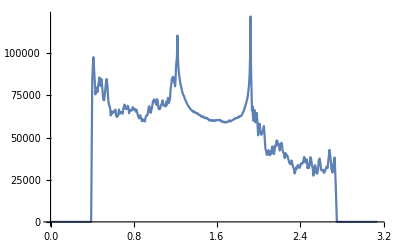

```mathematica
ListPlot[livetimeFull[[;;,2;;3]],Joined->True]
```

```mathematica
B8shapeData = Import[NotebookDirectory[]<>"Data/SNO phase 1/0003006.csv"];
Do[B8shapeData[[i,2]]=Max[0,B8shapeData[[i,2]]],{i,Length[B8shapeData]}];
B8shape = Interpolation[B8shapeData,InterpolationOrder->1];
```

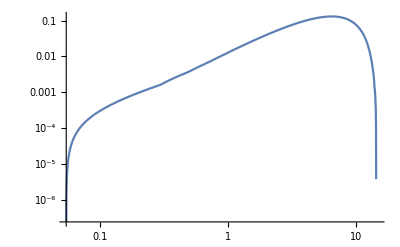

```mathematica
LogLogPlot[B8shape[e],{e,First[B8shapeData][[1]],Last[B8shapeData][[1]]}]
```

```mathematica
NIntegrate[B8shape[e],{e,First[B8shapeData][[1]],Last[B8shapeData][[1]]}]
```

0.995954

```mathematica
CCCrossSectionData = Import[NotebookDirectory[]<>"Data/SNO phase 1/0008032TableII.csv"];
```

```mathematica
L1A = 5.6; (* fm^3 *)
CCCrossSection = Interpolation[Table[{CCCrossSectionData[[i,1]],CCCrossSectionData[[i,2]] + L1A * CCCrossSectionData[[i,3]]},{i,Length[CCCrossSectionData]}],InterpolationOrder->1] (* 10^-42 cm^2 *)
```

InterpolatingFunction[…]

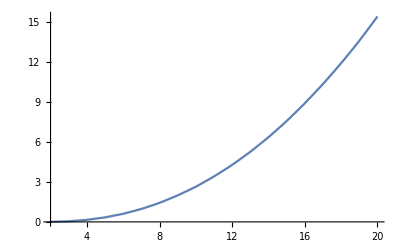

```mathematica
Plot[CCCrossSection[e],{e,First[CCCrossSectionData][[1]],Last[CCCrossSectionData][[1]]}]
```

```mathematica
σT[Te_] := -0.0684 + 0.331 √Te + 0.0425 Te;
ΔT = 0;
CCDetectorResponse[Teff_, Te_] :=1/(√(2Pi) σT[Te]) Exp[-(Teff - Te - ΔT)^2/(2 σT[Te]^2)];
```

```mathematica
CCCrossSectionDetector[Teff_] := NIntegrate[CCCrossSection[Te] CCDetectorResponse[Teff, Te],{Te,0,Infinity}]
```

InterpolatingFunction::dmval: Input value {0.000408571} lies outside the range of data in the interpolating function. Extrapolation will be used.

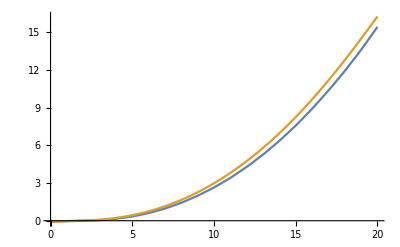

```mathematica
Plot[{CCCrossSection[e],test[e]},{e,0,20}]
```

```mathematica
NIntegrate[CCCrossSection[Te] CCDetectorResponse[Teff, Te],{Te,0,Infinity}]
```

Electron neutrino survival probability as a function of mixing parameters, energy and η

```mathematica
Pee[th12_,th13_,th23_,dm12_, dm3l_,d_,energy_,eta_]:=Module[{temp=Utilde[th13,th12,dm12, dm3l,energy,eta]},
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
Abs[(r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]]))[[1]]]^2]
```

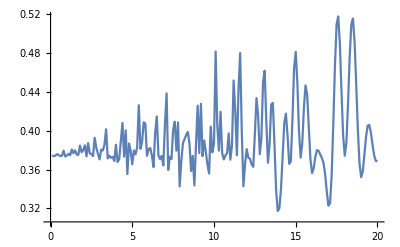

```mathematica
ListPlot[Table[{energy,Pee[th12,th13,th23,dm12, dm3l,d,energy MeV ,0]},{energy, 0.1,20,0.1}],Joined->True]
```

```mathematica
Pee[th12,th13,th23,dm12, dm3l,d,energy ,eta]
```

0.306027

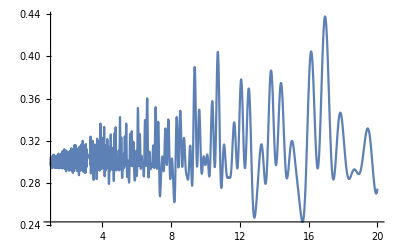

```mathematica
Plot[Pee[th12,th13,th23,dm12, dm3l,d,energy MeV,0],{energy,1 ,20}]
```

```mathematica
Pee[th12,th13,th23,dm12, dm3l,d,10 MeV,Pi]
```

0.296942

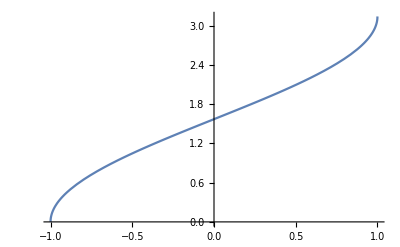

```mathematica
Plot[Pi-ArcCos[cz],{cz,-1 ,1}]
```

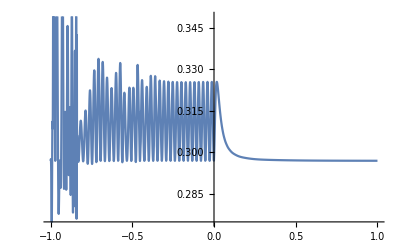

```mathematica
Plot[Pee[th12,th13,th23,dm12, dm3l,d,10 MeV,Pi - ArcCos[cz]],{cz,-1 ,1}]
```

```mathematica
eta
```

0.460235

```mathematica
temp=Utilde[th13,th12,dm12, dm3l,energy,eta];
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]])
```

{0.581628+0.120418 ⅈ,0.553995+0.134873 ⅈ,-0.555968-0.114051 ⅈ}

```mathematica
energy
```

10.0792 MeV

```mathematica
Table[{zenithList[[i]],livetime[[i]][[1]]},{i,Length[livetime]}]
```

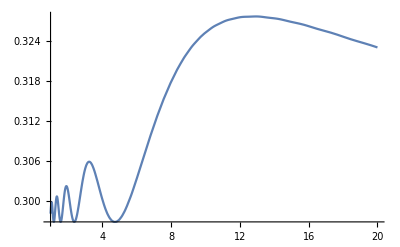

```mathematica
Plot[PeesolarHorizon[e],{e,1,20}]
```

```mathematica
PB8Horizon=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8data[[All,1]]}];
```

```mathematica
temp=Utilde[th13,th12,dm12, dm3l,20 MeV,Pi/2];
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]])
Abs[%[[2]]]^2
```

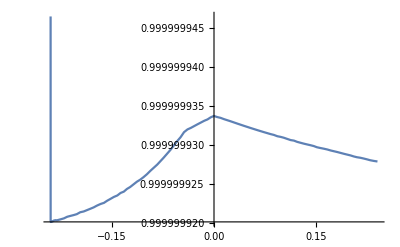

```mathematica
Plot[Evaluate[Abs[nue[x]]^2+Abs[numu[x]]^2+Abs[nutau[x]]^2/.s],{x,t1,t2}]
```

```mathematica
rE^2/60 V[0.192^4(5 β[[1]]+2γ[[1]](2 0.192^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]
```

{{0.,-0.00312091,0.},{0.00312091,0.,0.},{0.,0.,0.}}

```mathematica
(0.192 rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[0.192]*mol/cm^3])
```

{{2.95132,0.521283,0.},{0.521283,3.00811,0.},{0.,0.,309.845}}

```mathematica
Timing[(MatrixExp[- I(0.192 rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[0.192]*mol/cm^3])-rE^2/60 V[0.192^4(5 β[[1]]+2γ[[1]](2 0.192^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]].(PMNS[th12,th13,th23,d]†[[2,;;]]))]
```

{0.000432,{-0.227292+0.455301 ⅈ,-0.860404-0.0272839 ⅈ,0.+0. ⅈ}}

InterpolatingFunction::dmval: Input value {3.92229×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

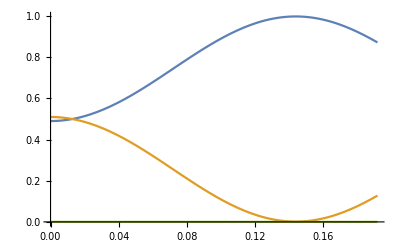

```mathematica
Plot[Evaluate[Abs[(MatrixExp[- I(x rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[x]*mol/cm^3])-rE^2/60 V[x^4(5 β[[1]]+2γ[[1]](2x^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]].(PMNS[th12,th13,th23,d]†[[2,;;]]))]^2],{x,0,0.192}]
```

```mathematica
N0int[x_]:= NIntegrate[Ne[r],{r,0,x}]/x
```

```mathematica
n0tab = Table[{x,N0int[x]},{x,0.01,1,0.01}];
```

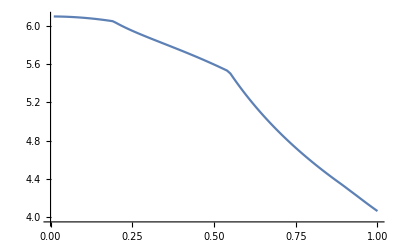

```mathematica
ListPlot[n0tab,Joined->True]
```

```mathematica
n0int=Interpolation[n0tab]
```

InterpolatingFunction[…]

```mathematica
n0int[0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

6.099

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

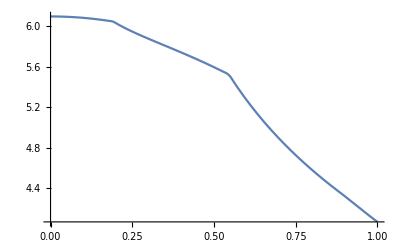

```mathematica
Plot[n0int[x],{x,0,1}]
```

```mathematica
(* comparisons *)
```

```mathematica
Hint[th_, δm2_, e_, η_] :=Module[{n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},
rE/2*m{
{ V[n*(mol/cm^3)]-x k[δm2,e] Cos[2th],x k[δm2,e] Sin[2th]},
{x k[δm2,e] Sin[2th],x k[δm2,e] Cos[2th] - V[n*(mol/cm^3)]}
}/2];
```

```mathematica
U2[th_, δm2_, e_, η_]:=Module[{u=MatrixExp[-I Hint[th,δm2,e, η]]},u.uᵀ]
```

```mathematica
Pe[th_,δm2_,e_, η_]:= Module[{Uee = U2[th,δm2,e, η]}, Abs[Uee[[1,1]] Sin[th] + Uee[[1,2]] Cos[th]]^2]
```

```mathematica
PS[th_, δm2_,e_] := NIntegrate[Pveve[th,0,δm2,10^4 eV^2,e,density[r]]*B8radial[r]/B8int,{r,0,0.5}];
```

```mathematica
PSE[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = Pe[th,δm2,e,η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
P2eSolar[th_, δm2_,e_,η_]:=Module[{n=NchordInt[η]/(Last[xj[η]]+Δx[η]/rE),x=Last[xj[η]]+Δx[η]/rE},Sin[th]^2*(1+(4/((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)) *(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2*Sin[k[δm2,e]*((rE x m)/2)*√((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)]^2 )]
```

```mathematica
P2eSolar2[th_, δm2_,e_,n_,l_]:=Sin[th]^2*(1+(4/((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)) *(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2*Sin[k[δm2,e]*(l/2 m)*√((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)]^2 )
```

```mathematica
PSE2[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = P2eSolar[th,δm2,e,η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
PSE3[th12_,th13_, Δms21_,Δms31_,e_,n_,l_] := Module[{ps = PS[th12, Δms21,e],cos12Mbar = NIntegrate[Cos[2 th12M[th12,th13,Δms21,Δms31,e,density[r]]]*B8radial[r]/B8int,{r,0,0.5}]},ps - Cos[th13]^2 cos12Mbar*(P2eSolar2[th12,Δms21,e,n,l] - Sin[th12]^2)]
```

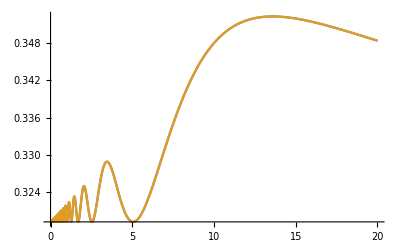

```mathematica
Plot[{Pe[ArcTan[√0.469], 7.9 10^-5 eV^2, e MeV, Pi/2],P2eSolar[ArcTan[√0.469], 7.9 10^-5 eV^2, e MeV,Pi/2]},{e,0,20}]
```

```mathematica
list=Table[{e,PSE2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, Pi/2]},{e,0.1,20,0.05}];
list2=Table[{e,PSE2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, Pi]},{e,0.1,20,0.05}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.561184 and 1.37682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.559777 and 1.37685×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.561184 and 1.37682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.559777 and 1.37685×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
(* OK, now compare with numerical solution *)
```

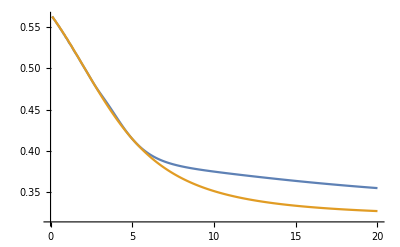

```mathematica
ListPlot[{list,list2},Joined->True]
```

```mathematica
H[r_,th_, δm2_, e_] := {
{V[Ne[r]*(mol/cm^3)] - k[δm2,e] Cos[2th], k[δm2,e] Sin[2th]},
{k[δm2,e] Sin[2th], k[δm2,e] Cos[2th] - V[Ne[r]*(mol/cm^3)]}
}/2;
```

```mathematica
N0int[0.5]
```

5.59659

```mathematica
U2[th_, δm2_, e_, n_,L_]:=Module[{u=MatrixExp[-I Hnu2[th,δm2,e, n]*L]},u]
```

```mathematica
Uconst[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, n_,L_]:=Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ],u=MatrixExp[-I Htilde[th13,th12,Δms21,Δms3l,E, n]*L]},
Chop[r23.d.u.d*.r23ᵀ]]
```

```mathematica
U[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, η_]:= Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ],n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},
r23.d.MatrixExp[- I *rE*m(x*r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ + DiagonalMatrix[{V[n*mol/cm^3],0,0}])].d*.r23ᵀ
]
```

```mathematica
U2[th12,10^-5 eV^2,10 MeV,NchordInt[0] mol/cm^3, rE m]//MatrixForm
```

(-0.908167+0.0549061 ⅈ | 0.20281+0.362059 ⅈ
0.20281+0.362059 ⅈ | -0.521183+0.745754 ⅈ)

```mathematica
Uconst[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV, NchordInt[0] mol/cm^3, rE m]//MatrixForm
```

(-0.908167+0.0549061 ⅈ | 0.20281+0.362059 ⅈ | 0
0.20281+0.362059 ⅈ | -0.521183+0.745754 ⅈ | 0
0 | 0 | 0.536659+0.843799 ⅈ)

```mathematica
U[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV,0]//MatrixForm
```

(-0.907582+0.055344 ⅈ | 0.204325+0.362607 ⅈ | 0.+0. ⅈ
0.204325+0.362607 ⅈ | -0.51747+0.747658 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.878671+0.477427 ⅈ)

```mathematica
(* Check the integration *)
```

```mathematica
Hnu[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_,n_]:=Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ]},
Chop[r23.d.(r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ+DiagonalMatrix[{V[n],0,0}]).d*.r23ᵀ]]
```

```mathematica
Hnu2[th_,Δms_,E_,n_]:=Module[{u={{Cos[th],Sin[th]},{-Sin[th],Cos[th]}}},Chop[u.DiagonalMatrix[{0,k[Δms,E]}].uᵀ+DiagonalMatrix[{V[n],0}]]]
```

```mathematica
Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2, 10 MeV, 6 mol/cm^3]*10^3 m//MatrixForm
```

(0.00485183 | 0.0000706251 | 0
0.0000706251 | 1.9707×10^-6 | 0
0 | 0 | 0.2533)

```mathematica
Pe[th12,10^-5 eV^2,10 MeV, 0]
```

0.487244

```mathematica
Abs[Pconst[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV, NchordInt[0] mol/cm^3, rE m]]^2//MatrixForm
```

(0.512085 | 1.01662×10^-6 | 0
1.01662×10^-6 | 0.512085 | 0
0 | 0 | 1.)

```mathematica
Abs[U[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV,0]]^2//MatrixForm
```

(0.663057 | 0.336943 | 0.
0.336943 | 0.663057 | 0.
0. | 0. | 1.)

```mathematica
HtildeInt[th13_,th12_,Δms21_,Δms3l_,E_, η_] := Module[{r13=R13[th13],r12=R12[th12],n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},rE*m(x*r13.r12.DiagonalMatrix[{0,k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ + DiagonalMatrix[{V[n*(mol/cm^3)],0,0}])];
```

```mathematica
xj[0]
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
Δx[0]/rE
```

0.000313922

```mathematica
U[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, η_]:=Module[{r23=R23[th23],d=Δ[δ],u=MatrixExp[-I HtildeInt[th13,th12,Δms21,Δms3l,E, η]]},
(r23.d.u.d*.r23ᵀ)]
```

```mathematica
Abs[U2[th12,7.9 10^-5 eV^2, 10 MeV, 0]]^2//MatrixForm
```

(0.977508 | 0.022492
0.022492 | 0.977508)

```mathematica
Abs[U[th13,th12,th23,0,7.9 10^-5 eV^2,100 eV^2,10 MeV,0]]^2//MatrixForm
```

(0.751406 | 0.248594 | 0.
0.248594 | 0.751406 | 0.
0. | 0. | 1.)

```mathematica
%235/%234[[1;;2,1;;2]]//MatrixForm
```

(1.15224+0.279683 ⅈ | -0.492132-0.662986 ⅈ
-0.492132-0.662986 ⅈ | -0.06585+1.18387 ⅈ)

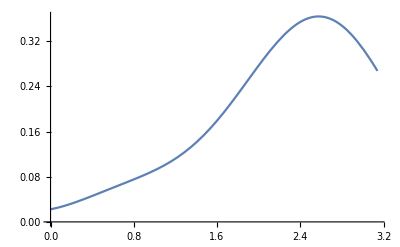

```mathematica
Plot[Abs[U[33 Degree,45 Degree,30 Degree, η, 10^-5 eV^2, 10^-3 eV^2, 10 MeV, Pi/2][[1,2]]]^2,{η,0,Pi}]
```

```mathematica
Sin[45 Degree]^2
```

1/2

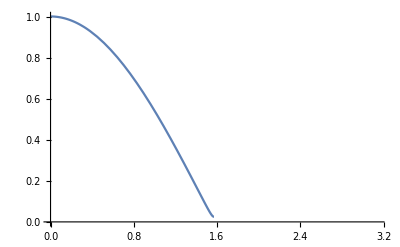

```mathematica
Plot[Last[xj[η]]+Δx[η]/rE,{η,0,Pi}]
```

```mathematica
V[100 mol/cm^3]
```

0.00003868/m

```mathematica
MatrixExp[-I 100  m*Htilde[33 Degree, 45 Degree, 10^-5 eV^2, 10^-3 eV^2, 100 mol/cm^3, 10 MeV]//Chop]//MatrixForm
```

(0.999868-0.0114696 ⅈ | -2.18873×10^-7-0.000106217 ⅈ | -0.000168782-0.0115107 ⅈ
-2.18873×10^-7-0.000106217 ⅈ | 1.-0.00012665 ⅈ | 8.74196×10^-9+0.0000689793 ⅈ
-0.000168782-0.0115107 ⅈ | 8.74196×10^-9+0.0000689793 ⅈ | 0.999774-0.0178519 ⅈ)

```mathematica
(* Check with 3 flavour *)
```

```mathematica
list=Table[{e,PSE3[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2, 2.46 10^-3 eV^2, e MeV, 1.35, 200 10^3]},{e,0.1,20,0.05}];
list2=Table[{e,PSE3[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2, 2.46 10^-3 eV^2, e MeV, 0.5, 200 10^3]},{e,0.1,20,0.05}];
```

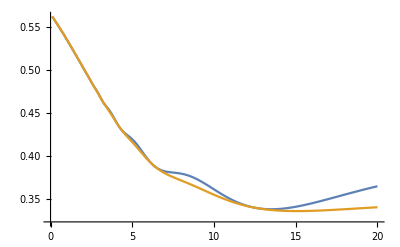

```mathematica
ListPlot[{list,list2},Joined->True]
```

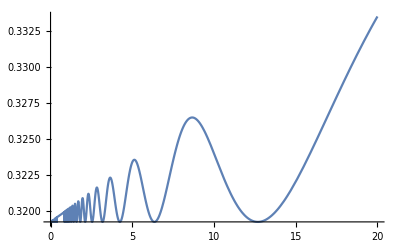

```mathematica
Plot[P2eSolar2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, 0.5, 200 10^3],{e,0,20}]
```

```mathematica
NchordInt[Pi/2]/(Last[xj[Pi/2]]+Δx[Pi/2]/rE)
```

1.66967

```mathematica
(Last[xj[Pi/2]]+Δx[Pi/2]/rE)
```

0.0250549

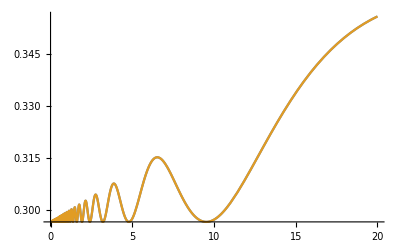

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2,e MeV, Pi/2],P2eSolar[33 Degree,7.5 10^-5 eV^2,e MeV, Pi/2]},{e,0,20}]
```

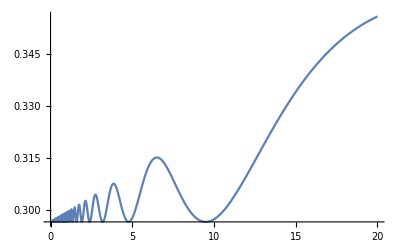

```mathematica
Plot[P2eSolar2[33 Degree,7.5 10^-5 eV^2, e MeV,1.67, 159 10^3],{e,0,20}]
```

```mathematica
Pe[33 Degree,7.5 10^-5 eV^2, 10 MeV,0]
```

0.353663

```mathematica
NchordInt[Pi/2]
```

0.0418332

```mathematica
Last[xj[Pi/2]]
```

0

```mathematica
N[Pi/2]
```

1.5708

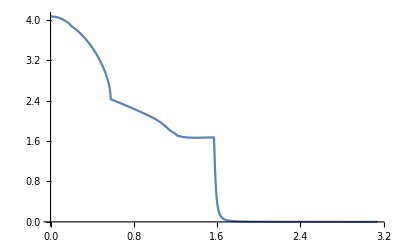

```mathematica
Plot[NchordInt[η]/(Last[xj[η]]+Δx[η]/rE),{η,0,Pi},Exclusions->None]
```

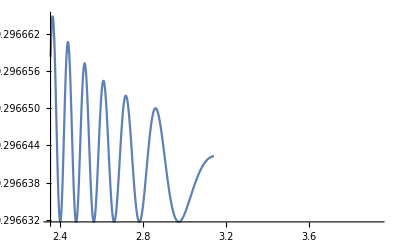

```mathematica
Plot[P2eSolar[33 Degree,7.9 10^-5 eV^2,20 MeV,η],{η,1.5 Pi/2,2.5 Pi/2}]
```

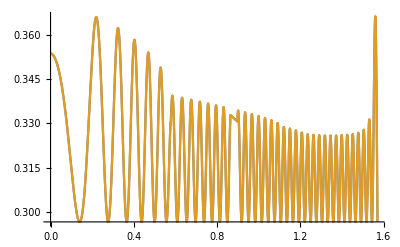

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2, 10 MeV,η],P2eSolar[33 Degree,7.5 10^-5 eV^2, 10 MeV,η]},{η,0,Pi/2}]
```

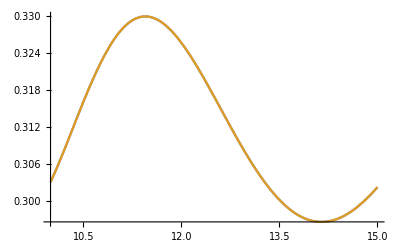

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2, e MeV,Pi/2.1],P2eSolar[33 Degree,7.5 10^-5 eV^2, e MeV,Pi/2.1]},{e,10,15}]
```

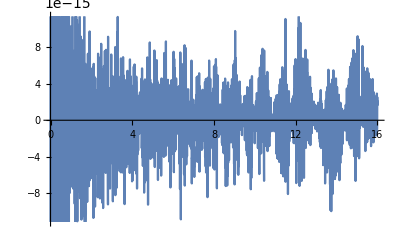

```mathematica
Plot[2(P2eSolar[33 Degree,1.5 10^-5 eV^2, e MeV,0]-Pe[33 Degree,1.5 10^-5 eV^2, e MeV,0])/(P2eSolar[33 Degree,1.5 10^-5 eV^2, e MeV,0]+Pe[33 Degree,1.5 10^-5 eV^2, e MeV,0]),{e,0,16}]
```

```mathematica
Timing[Nint[Pi/2.1]]
```

{0.50969,0.124662}

```mathematica
3^3
```

27

```mathematica
xj[0]
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
Last[xj[Pi/2.1]]
```

0.0747301

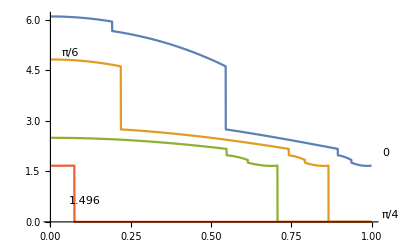

```mathematica
Plot[{Nchord[0,x],Nchord[Pi/6,x],Nchord[Pi/4,x],Nchord[Pi/2.1,x]},{x,0,1},Exclusions->None, PlotLabels->Placed[{0, Pi/6, Pi/4, Pi/2.1},{Automatic,Above}]]
```

```mathematica
Nint[η_] := Integrate[Nchord[η,x],{x,0,1}];
```

```mathematica
Nint[Pi/2.1]/0.074
```

1.68462

```mathematica
Clear[Nint]
```

```mathematica
n=4 10^3;
Δr = 1/n;
```

```mathematica
list = Table[Chop[MatrixExp[-I (rE*Δr)H[i Δr,33 Degree, 10^-5 eV^2, 10MeV]]],{i,n,-n,-1}];
```

```mathematica
Ugen[r0_,r1_,th_, δm2_, e_]:=MatrixExp[-I rE Integrate[H[r,th,δm2,e],{r,r0,r1}]]
```

```mathematica
U[-1,-1+10Δr,33 Degree, 10^-5 eV^2, 10MeV]
```

{{0.999825+0.00306766 ⅈ,-1.30742×10^-21-0.0184477 ⅈ},{1.53833×10^-21-0.0184477 ⅈ,0.999825-0.00306766 ⅈ}}

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

{{-0.162396-0.103592 ⅈ,-7.63278×10^-17+0.981273 ⅈ},{-3.46945×10^-17+0.981273 ⅈ,-0.162396+0.103592 ⅈ}}

```mathematica
list[[-10;;-1]]
```

{{0.999998+0.00082139 ⅈ,0.-0.00184487 ⅈ},{0.-0.00184487 ⅈ,0.999998-0.00082139 ⅈ}}

```mathematica
Apply[Dot,list[[-10;;-1]]]
```

{{0.999823+0.0035822 ⅈ,-8.5274×10^-6-0.0184477 ⅈ},{8.5274×10^-6-0.0184477 ⅈ,0.999823-0.0035822 ⅈ}}

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

{{-0.647149+0.0800368 ⅈ,2.77556×10^-17-0.758151 ⅈ},{0.-0.758151 ⅈ,-0.647149-0.0800368 ⅈ}}

```mathematica
H[0,33 Degree, 10^-5 eV^2, 10MeV]
```

{{(6.64415×10^-7)/m,(1.15701×10^-6)/m},{(1.15701×10^-6)/m,-(6.64415×10^-7)/m}}

```mathematica
Nint
```

4.064

```mathematica
Ugen[0,1,33 Degree, 10^-5 eV^2, 10MeV]
```

{{0.271536-0.219366 ⅈ,0.-0.937095 ⅈ},{0.-0.937095 ⅈ,0.271536+0.219366 ⅈ}}

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

{{0.271536-0.219366 ⅈ,0.-0.937095 ⅈ},{0.-0.937095 ⅈ,0.271536+0.219366 ⅈ}}

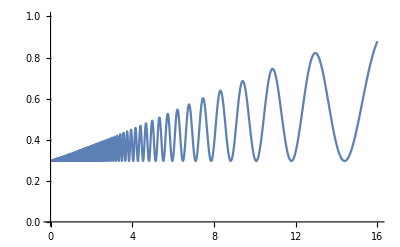

```mathematica
Plot[Pe[33 Degree,1.5 10^-5 eV^2, e MeV],{e,16,0.05},PlotRange->{Automatic,{0,1}}]
```

```mathematica
ArcSin[√0.64]/2/Degree
```

26.5651

```mathematica
Nint
```

8.128

```mathematica
list1=Table[{e,PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV]},{e,0.1,16,0.05}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.660949 and 1.09725×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.650227 and 1.41313×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.638675 and 1.34234×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
LMA = Interpolation[Import[NotebookDirectory[]<>"Data/9702343_LMA.csv"],InterpolationOrder->1];
```

InterpolatingFunction::dmval: Input value {0.000326857} lies outside the range of data in the interpolating function. Extrapolation will be used.

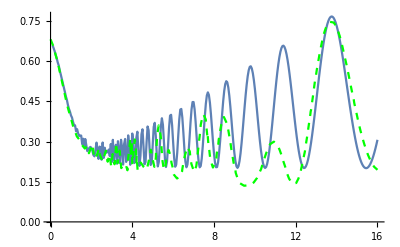

```mathematica
Show[ListPlot[list1,Joined->True],Plot[LMA[e],{e,0,16},PlotStyle->{Dashed,Green}]]
```

```mathematica
Nebar[η_]:=Table[((αp[η][[i]]*(xj[η][[i+1]]-xj[η][[i]]) + βp[η][[i]] (xj[η][[i+1]]^3-xj[η][[i]]^3)/3 + γp[η][[i]] (xj[η][[i+1]]^5-xj[η][[i]]^5)/5)/(xj[η][[i+1]]-xj[η][[i]]))*(mol/cm^3),{i,Length[xj[η]]-1}];
```

```mathematica
δNe[η_,x_]:=Piecewise[Table[{(αp[η][[i]] + βp[η][[i]] x^2 + γp[η][[i]] x^4)*(mol/cm^3) - Nebar[η][[i]],xj[η][[i]]≤x<xj[η][[i+1]]},{i,Length[xj[η]]-1}]];
```

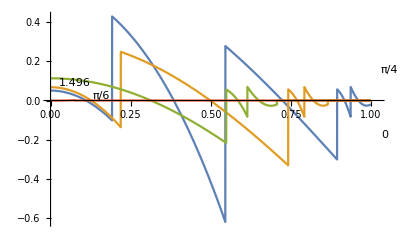

```mathematica
Plot[{δNe[0,x]/(mol/cm^3),δNe[Pi/6,x]/(mol/cm^3),δNe[Pi/4,x]/(mol/cm^3),δNe[Pi/2.1,x]/(mol/cm^3)},{x,0,1},Exclusions->None, PlotLabels->Placed[{0, Pi/6, Pi/4, Pi/2.1},{Automatic,Above}],PlotRange->All]
```

```mathematica
sin2thm[th_,δm2_,e_,Njbar_] := Sin[2th]/√((Cos[2th]-V[Njbar]/k[δm2,e])^2 + Sin[2th]^2);
cos2thm[th_,δm2_,e_,Njbar_] := √(1 - sin2thm[th,δm2,e,Njbar]^2);
km[th_,δm2_,e_,Njbar_] := k[δm2,e]*(Sin[2th]/sin2thm[th,δm2,e,Njbar]);

x[η_]:=Table[Mean[{xj[η][[i+1]],xj[η][[i]]}],{i,Length[xj[η]]-1}];
```

```mathematica
rE = 6.3781*10^6 m;
```

```mathematica
cj[th_,δm2_,e_,η_]:=Table[Cos[km[th,δm2,e,Nebar[η][[i]]]*(xj[η][[i+1]]-xj[η][[i]])rE/2],{i,Length[x[η]]}];
sj[th_,δm2_,e_,η_]:=Table[Sin[km[th,δm2,e,Nebar[η][[i]]]*(xj[η][[i+1]]-xj[η][[i]])rE/2],{i,Length[x[η]]}];
```

```mathematica
Cj0[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[Cos[kbar*r(x-xbar)],{x,x1,x2}]];
Cj2[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^2 Cos[kbar*r(x-xbar)],{x,x1,x2}]];
Cj4[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^4 Cos[kbar*r(x-xbar)],{x,x1,x2}]];

Sj0[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[Sin[kbar*r(x-xbar)],{x,x1,x2}]];
Sj2[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^2 Sin[kbar*r(x-xbar)],{x,x1,x2}]];
Sj4[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^4 Sin[kbar*r(x-xbar)],{x,x1,x2}]];
```

```mathematica
?Cj0
```

```mathematica
Cj[th_,δm2_,e_,η_]:=rE*Table[V[(αp[η][[i]]*(mol/cm^3)-Nebar[η][[i]])]*Cj0[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
 V[βp[η][[i]]*(mol/cm^3)]*Cj2[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
V[γp[η][[i]]*(mol/cm^3)]*Cj4[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE] ,{i,Length[xj[η]]-1}];
Sj[th_,δm2_,e_,η_]:=rE*Table[V[(αp[η][[i]]*(mol/cm^3)-Nebar[η][[i]])]*Sj0[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
 V[βp[η][[i]]*(mol/cm^3)]*Sj2[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
V[γp[η][[i]]*(mol/cm^3)]*Sj4[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE] ,{i,Length[xj[η]]-1}];
```

```mathematica
Uj[th_,δm2_,e_,η_]:= Chop[Module[{c=cj[th,δm2,e,η], s=sj[th,δm2,e,η],C=Cj[th,δm2,e,η],S=Sj[th,δm2,e,η],c2thm = cos2thm[th,δm2,e,Nebar[η]], s2thm = sin2thm[th,δm2,e,Nebar[η]]},
Table[{
{c[[i]] + I s[[i]]*c2thm[[i]], - I s[[i]]*s2thm[[i]]},
{- I s[[i]]*s2thm[[i]], c[[i]] - I s[[i]]*c2thm[[i]]}
}
 - (I/2)*s2thm[[i]]*{
{C[[i]]*s2thm[[i]], C[[i]]*c2thm[[i]] - I S[[i]]},
{C[[i]]*c2thm[[i]] + I S[[i]], -C[[i]]*s2thm[[i]]} 
} ,{i,Length[xj[η]]-1}]]];
```

```mathematica
Table[{e,Abs[UIF[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}]
```

{{0.1,0.602717},{1.1,0.766273},{2.1,0.986437},{3.1,0.911325},{4.1,0.93176},{5.1,0.226402},{6.1,0.987274},{7.1,0.371808},{8.1,0.936275},{9.1,0.902174},{10.1,0.326585},{11.1,0.850086},{12.1,0.634817},{13.1,0.985292},{14.1,0.593789},{15.1,0.789022}}

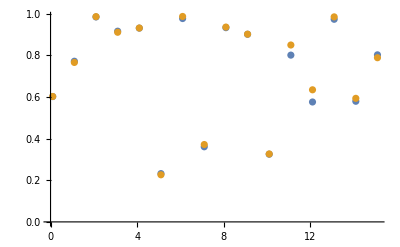

```mathematica
ListPlot[{%440,%442}]
```

```mathematica
Table[{e,Abs[UIF[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}]
```

{{0.1,0.602355},{1.1,0.772053},{2.1,0.984851},{3.1,0.916469},{4.1,0.931154},{5.1,0.232103},{6.1,0.977291},{7.1,0.361015},{8.1,0.933496},{9.1,0.901642},{10.1,0.325233},{11.1,0.801468},{12.1,0.576235},{13.1,0.973739},{14.1,0.579746},{15.1,0.802876}}

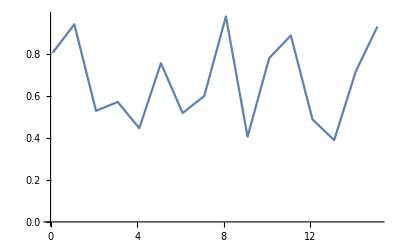

```mathematica
ListPlot[Table[{e,Abs[U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}],Joined->True]
```

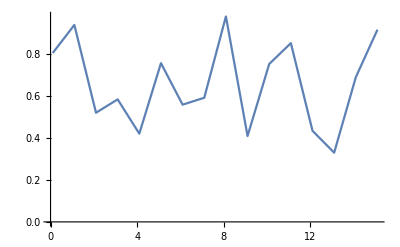

```mathematica
ListPlot[Table[{e,Abs[U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}],Joined->True]
```

```mathematica
U0F[th_,δm2_,e_,η_]:=Chop[ Module[{list = Table[Uj[th,δm2,e,η][[i]],{i,Length[xj[η]]-1}]}, Apply[Dot,list]]];
UIF[th_,δm2_,e_,η_]:=Chop[Module[{u = U0F[th,δm2,e,η]},u.uᵀ]];
```

```mathematica
Pe[th_,δm2_,e_,η_]:= Module[{Uee = UIF[th,δm2,e,η]}, Abs[Uee[[1,1]] Sin[th] + Uee[[1,2]] Cos[th]]^2]
```

```mathematica
PS[th_, δm2_,e_] := NIntegrate[Pveve[th,0,δm2,100 eV^2,e,density[r]]*B8radial[r]/B8int,{r,0,0.5}];
```

```mathematica
PSE[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = Pe[th,δm2,e, η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14 MeV,0] //MatrixForm
```

(-0.726837-0.225548 ⅈ | 0.0804613+0.64371 ⅈ
-0.0804613+0.64371 ⅈ | -0.726837+0.225548 ⅈ)

```mathematica
LMA = Interpolation[Import[NotebookDirectory[]<>"Data/9702343_LMA.csv"],InterpolationOrder->1];
```

```mathematica
pseLarge = Table[{e,PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV, 0]},{e,0.1,16,0.1}];
psLarge = Table[{e,PS[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV]},{e,0.1,16,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.660949 and 1.09725×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.638675 and 1.34234×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.613043 and 1.48939×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.660949 and 1.09725×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.638675 and 1.34234×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.613043 and 1.48939×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

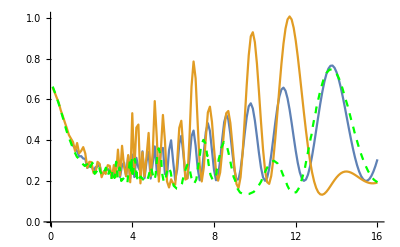

```mathematica
Show[ListPlot[{list,pseLarge},Joined->True],Plot[LMA[e],{e,0.1,16},PlotStyle->{Green,Dashed}]]
```

```mathematica
Timing[PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV, 0]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.201364 and 4.91638×10^-7 for the integral and error estimates.

{1.099,0.880687}

```mathematica
Timing[pSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV]]
```

```mathematica
(* Numerical integration seem to be faster! *)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.201364 and 4.91638×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.546859}. NIntegrate obtained -4.51387 and 0.00163321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.546859}. NIntegrate obtained 4.51387 and 0.00163321 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.331038,0.497289}

```mathematica
Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV,0]
```

0.82754

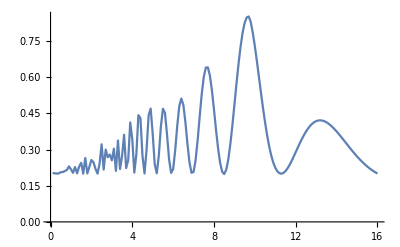

```mathematica
ListPlot[Table[{e,Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]},{e,0.1,16,0.1}],Joined->True]
```

InterpolatingFunction::dmval: Input value {0.000326857} lies outside the range of data in the interpolating function. Extrapolation will be used.

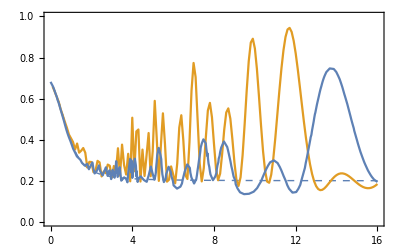

```mathematica
Show[ListPlot[{psLarge,pseLarge},Joined->True,PlotRange->{Automatic,{0,1}},PlotStyle->{{Thin,Dashed},Automatic}],Plot[LMA[e],{e,0,16}],Frame->True]
```

```mathematica
pseSmall = Table[{e,PSE[ArcSin[√(8.1 10^-3)]/2,5.2 10^-6 eV^2, e MeV, 0]},{e,0.1,16,0.1}];
psSmall = Table[{e,PS[ArcSin[√(8.1 10^-3)]/2,5.2 10^-6  eV^2, e MeV]},{e,0.1,16,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.99424 and 2.42757×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.988761 and 1.69346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.943223 and 7.9555×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.99424 and 2.42757×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.988761 and 1.69346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.943223 and 7.9555×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

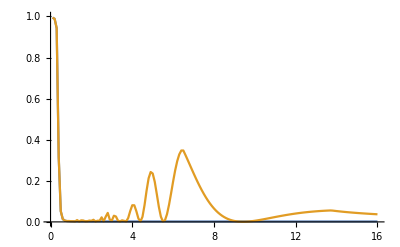

```mathematica
ListPlot[{psSmall,pseSmall},Joined->True,PlotRange->{Automatic,{0,1}}]
```

```mathematica
hbar = {
{√2 Gf Nbar - kk Cos[2th], kk Sin[2th]},
{kk Sin[2th], kk Cos[2th] - √2 Gf Nbar}
}/2;
δh = Gf DiagonalMatrix[{δN,-δN}]/√2;
```

```mathematica
MatrixExp[-I hbar r (xi-xi1)]//Simplify
```

{{(ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar+ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])),-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))},{-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])),(ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))}}

```mathematica
MatrixForm[%]
```

((ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar+ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) | -(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))
-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) | (ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))

```mathematica
MatrixExp[-I hbar  r(xi-xx)].δh.MatrixExp[-I hbar r (xx-xi1)]//Simplify
```

{{(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ kk Cos[2 th] (ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])),-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))},{-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]-ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th]))),-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2-2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ kk Cos[2 th] (-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))}}

```mathematica
MatrixForm[%]
```

((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ kk Cos[2 th] (ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])) | -(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th]))
-(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]-ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])) | -(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2-2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ kk Cos[2 th] (-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))

```mathematica
rj
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
nbar = NIntegrate[Ne[r],{r,0,rj[[3]]}]/rj[[3]]*(mol/cm^3)
```

(5.52287 mol)/cm^3

```mathematica
Nebar[0]
```

{(6.04839 mol)/cm^3,(5.23784 mol)/cm^3,(2.46815 mol)/cm^3,(1.92156 mol)/cm^3,(1.68921 mol)/cm^3}

```mathematica
rE
```

6.3781×10^6 m

```mathematica
H[th_,δm2_,e_, N_] := {
{V[N*(mol/cm^3)]-k[δm2,e]Cos[2th], k[δm2,e]Sin[2th]},
{k[δm2,e] Sin[2th],k[δm2,e] Cos[2th]-V[N*(mol/cm^3)]}
}/2;
```

```mathematica
u[th_,δm2_,e_] := MatrixExp[- I NIntegrate[rE H[th,δm2,e,Ne[r]],{r,-1,1}]];
p[th_,δm2_,e_] := Module[{uu=u[th,δm2,e]},Abs[uu[[1,1]] Sin[th]+uu[[1,2]]Cos[th]]^2]
pSE[th_, δm2_,e_] := Module[{ps = PS[th,δm2,e], pe = p[th,δm2,e]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
list = Table[{e,pSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2,e MeV]},{e,1,16,0.1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0419844}. NIntegrate obtained 0.391992 and 3.08945×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.546859}. NIntegrate obtained -135.375 and 0.00163321 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.546859}. NIntegrate obtained 135.375 and 0.00163321 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.000326857} lies outside the range of data in the interpolating function. Extrapolation will be used.

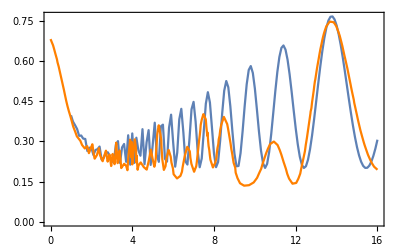

```mathematica
Show[ListPlot[list,Joined->True],Plot[LMA[e],{e,0,16},PlotStyle->Orange],Frame->True]
```

```mathematica
u[th_,δm2_,e_] :=Module[{uu=MatrixExp[- I H[th,δm2,e] rE rj[[3]]]},uu.uuᵀ];
```

```mathematica
p[th_,δm2_,e_] := Abs[u[th,δm2,e][[1,1]] Sin[th]+u[th,δm2,e][[1,2]]Cos[th]]^2
```

```mathematica
pse[th_, δm2_,e_] := Module[{ps = 0.2, pe = p[th,δm2,e]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
U0F[th_,δm2_,e_,η_]:=Chop[ Module[{list = Table[Uj[th,δm2,e,η][[i]],{i,2}]}, Apply[Dot,list]]];
```

```mathematica
Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14  MeV,0]
```

0.374943

```mathematica
p[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14  MeV]
```

0.940409

```mathematica
list1 = Table[{e,Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e  MeV,0]},{e,1,16,0.1}];
list2 = Table[{e,p[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e  MeV]},{e,1,16,0.1}];
```

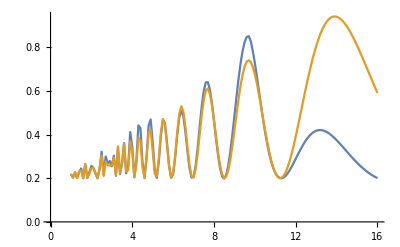

```mathematica
ListPlot[{list1,list2},Joined->True]
```